```mathematica
Exit[]
ClearAll["Global`*"]
```

```mathematica
<<SerialIO`
```

```mathematica
Names["SerialIO`*"]
arduino=SerialOpen["COM3"]
SerialSetOptions[arduino,"BaudRate"->19200];
read[serial_]:=Module[{count},data=ToCharacterCode[SerialRead[serial]][[1;;15]];
count=FromCharacterCode[Take[data,{Position[data,10][[1]][[1]]+1,Position[data,10][[2]][[1]]-2}]];
count]
h=910;l=735;
```

{SerialClose,SerialOpen,SerialPort,SerialRead,SerialReadyQ,SerialSetOptions,SerialWrite}

SerialPort[<COM3>]

```mathematica
s={};Tt0=AbsoluteTime[]; x=0;
RunScheduledTask[AppendTo[s,{read[arduino],AbsoluteTime[]-Tt0}];If[x≥1,RemoveScheduledTask[$ScheduledTask]],0.005];
```

```mathematica
x=2;
```

```mathematica
b1b
```

{2.57767}

{1.64938}

910

735

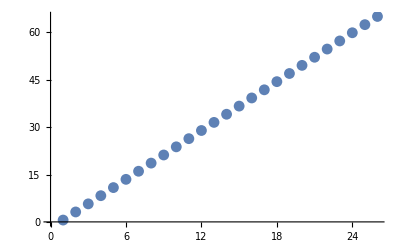

```mathematica
Export["D:\\Downloads\\data2.dat",s,"Data"];
SetDirectory["D:\\Downloads\\datafiles"];
(*ffm=FileNames["*.dat"]*)
(*Length[ffm]*)
b1b=Import["D:\\Downloads\\data2.dat","Table"];
(*Length[b1b]*)
b1bm=DeleteCases[Table[If[Length[b1b[[n]]]==2&&b1b[[n,1]]∈Reals&&s[[n,2]]∈Reals,{b1b[[n]][[2]],b1b[[n]][[1]]}],{n,1,Length[b1b]}],Null];
b1bx=Table[If[b1bm[[i,2]]>950,{b1bm[[i,1]],1},{b1bm[[i,1]],0}],{i,1,Length[b1bm]}];
b1bf=DeleteCases[Table[If[b1bx[[n,2]]==0,{b1bx[[n]][[1]]}],{n,1,Length[b1bx]}],Null];
b1bg=DeleteCases[Table[If[b1bf[[n+1,1]]-b1bf[[n,1]]>0.5,{b1bf[[n,1]]}],{n,1,Length[b1bf]-1}],Null];
b1bper=Table[{b1bg[[2i-1]],b1bg[[2i]]},{i,1,Length[b1bg]/2}];
last=Table[b1bper[[i,1,1]],{i,1,Length[Flatten[b1bper]]/2}];
T=(b1bper[[Length[b1bper],1]]-b1bper[[1,1]])/(Length[b1bper]-1)
L=(g T^2)/(4 π^2)/.g->9.8
h
l
Export["D:\\Downloads\\datafiles\\data1645pop.dat",{h,l,Table[last[[i]],{i,1,Length[b1bper]}],T,L},"Data"];
SerialClose[arduino]
ListPlot[Flatten[last]]
```

```mathematica
SerialClose[arduino]
```

SerialPort::inval: "588" is not a valid SerialPort identifier

$Failed